# Enhancing the SpokenString function output based on the input symbolic structure

Renan Germano

Mackenzie Presbyterian University

When dealing with graphs and images, the current SpokenString function returns a not significant text to the describe the input. The objective of the present project is to enhance this output by developing an algorithm that is capable of  better describing the input, based on its symbolic structure. Thinking about accessibility for visually impaired, this text could be used as an automatic generated alternative description for images and related contents.

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

### Some Experiments

#### Named Colors

```mathematica
?WolframLanguageData
```

```mathematica
wlEntityProperties=WolframLanguageData["Properties"]
```

{attributes,character count,common option values,date introduced,date last modified,dates modified,documentation basic examples,documentation example counts,documentation example inputs,documentation example text,entity classes,eponymous people,equal-precedence symbols,external links,frequencies of usage,full version introduced,full version last modified,full versions modified,functionality areas,symbol background,keyboard shortcuts,link trails,memberships,name,option names,options,plaintext usage,precedence ranks,ranks of usage,related entities,related guide pages,related symbols,relationship community graph,relationship graph,short notations,subject classifications,symbols linking to,symbols using as attribute,symbols using as option,text strings,timeline,timeline events,translations,typeset usage,URL,version introduced,version last modified,versions modified,Wolfram documentation link}

```mathematica
redNamedColorWLEntity=WolframLanguageData["Red"]
```

Red

```mathematica
entityPropertyValuesForRedColor={#,EntityValue[redNamedColorWLEntity, #]}&/@wlEntityProperties;
```

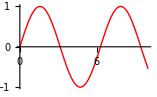
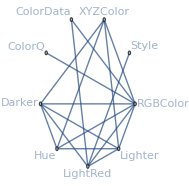
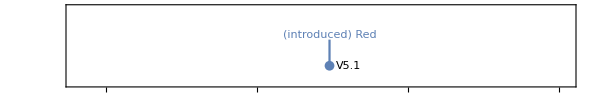
attributes | {Protected}
character count | 3
date introduced | Day: Mon 25 Oct 2004
documentation basic examples | {{Graphics[{Red,Disk[]}],-Graphics-,Plot[Sin[x],{x,0,10},PlotStyle→Red],-Graphics-,Graphics3D[{Red,Sphere[]}],-Graphics3D-}}
documentation example counts | {BasicExamples→1,Scope→0,GeneralizationsExtensions→0,Options→0,Applications→0,PropertiesRelations→0,PossibleIssues→0,InteractiveExamples→0,NeatExamples→0}
documentation example inputs | {BasicExamples→{{Graphics[{Red,Disk[]}],Plot[Sin[x],{x,0,10},PlotStyle→Red],Graphics3D[{Red,Sphere[]}]}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
documentation example text | {BasicExamples→{{}},Scope→{},GeneralizationsExtensions→{},Options→{},Applications→{},PropertiesRelations→{},PossibleIssues→{},InteractiveExamples→{},NeatExamples→{}}
entity classes | {Wolfram Language autoevaluating symbols}
eponymous people | {}
external links | {}
frequencies of usage | {All→0.000434382,StackExchange→0.00233259,TypicalProductionCode→0.0010278,WolframAlphaCodebase→0.0000142108,WolframDemonstrations→0.00218411,WolframDocumentation→0.00162619}
full version introduced | 5.1
functionality areas | {ColorSymbols}
symbol background | Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style[hello,Red]).
Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].
Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.
link trails | {{guide/WolframRoot,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GraphicsOptionsAndStyling,guide/Colors,ref/Red},{guide/WolframRoot,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/ImageProcessing,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ChartingAndInformationVisualization,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/3DPrinting,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/Finance,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ActuarialComputation,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Calculus,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/DateAndTime,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/EarthSciencesDataAndComputation,guide/GeographicData,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Finance,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/Geodesy,guide/LocationsPathsAndRouting,guide/MapsAndCartography,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/LifeSciencesAndMedicineDataAndComputation,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PeopleAndHistory,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/PlaneGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/ProbabilityAndStatistics,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/ScientificDataAnalysis,guide/Statistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polygons,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/SolidGeometry,guide/GeometricComputation,guide/Polyhedra,guide/SymbolicGraphicsLanguage,guide/GraphicsDirectives,guide/Colors,ref/Red},{guide/WolframRoot,guide/Statistics,guide/DescriptiveStatistics,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTime,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/DateAndTimeVisualization,guide/FinancialVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red},{guide/WolframRoot,guide/TimeSeries,guide/RandomVariables,guide/StatisticalVisualization,guide/DataVisualization,guide/ColorProcessing,guide/Colors,ref/Red}}
memberships | {Wolfram Language autoevaluating symbols}
name | Red
option names | {}
options | {}
plaintext usage | Red represents the color red in graphics or style specifications.
ranks of usage | {All→91,StackExchange→41,TypicalProductionCode→87,WolframAlphaCodebase→398,WolframDemonstrations→48,WolframDocumentation→54}
related entities | {red}
related guide pages | {Colorspaclet:guide/Colors,Symbolic Graphics Languagepaclet:guide/SymbolicGraphicsLanguage,Graphics Options & Stylingpaclet:guide/GraphicsOptionsAndStyling,Graphics Annotation & Appearancepaclet:guide/GraphicsAnnotationAndAppearance,Graphics Directivespaclet:guide/GraphicsDirectives,Maps & Cartographypaclet:guide/MapsAndCartography,Color Processingpaclet:guide/ColorProcessing,Notebook Formatting & Stylingpaclet:guide/NotebookFormattingAndStyling,Chart Styling & Layoutpaclet:guide/ChartLayoutAndStyling,Graph Visualizationpaclet:guide/GraphVisualization,Text Stylingpaclet:guide/TextStyling,GeoGraphics Languagepaclet:guide/GeoGraphicsLanguage,Graph Styling, Labeling, and Layoutpaclet:guide/GraphStylingAndLabeling,Maps & Cartographypaclet:guide/MapsAndGeographicData}
related symbols | {LightRed,ColorData,Lighter,Darker,Hue,RGBColor,Style}
relationship community graph | -Graphics-
relationship graph | -Graphics-
symbols linking to | {ColorQ,Hue,LightRed,RGBColor,XYZColor}
symbols using as attribute | {}
symbols using as option | {}
text strings | {Red represents the color red in graphics or style specifications.,Red is equivalent to RGBColor[1,0,0].,Red is a symbol that represents the color red in graphics or style specifications. Color specifications in the Wolfram Language can appear explicitly inside a Graphics or Graphics3D expression (e.g. Graphics[{Red,Disk[]}]), in which case they affect all subsequent expressions until another specification overrides them. They can also be used as part of an option specification, either singly (e.g. Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]) or as part of a Directive compound expression (e.g. Plot[Cos[x],{x,0,2Pi},PlotStyle->Directive[Thick,Red]]). Finally, they can appear inside Style wrappers that affect the appearance of text, equations, and notebook cells (e.g. Style["hello",Red]).,Red is a color located at one of the corners of the RGB color cube and evaluates to RGBColor[1,0,0].,Named symbols for other colors include Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple, as well as their LightRed etc. variants. Arbitrary colors can be input using Hue, RGBColor, CMYKColor, LABColor, LUVColor, or XYZColor. Colors can be modified using Lighter, Darker, and Blend. Colors may be converted between different systems using ColorConvert. The appearance of colors appearing in Graphics3D objects may be controlled using Glow, Specularity, and Lighting. The transparency of colored graphics objectives can be specified using Opacity. ColorData can be used to give a function that generates colors in a named color scheme.}
timeline | -Graphics-
timeline events | Day: Mon 25 Oct 2004Red
translations | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
typeset usage | Red represents the color red in graphics or style specifications. 
URL | http://reference.wolfram.com/language/ref/Red.html
version introduced | 5.1
Wolfram documentation link | Redpaclet:ref/Red

```mathematica
Grid[Select[entityPropertyValuesForRedColor, Not@MissingQ@Last@#&], Frame->All]
```

```mathematica
functionalityAreaOfAllWLSymbols={#, EntityValue[#,EntityProperty["WolframLanguageSymbol","FunctionalityAreas"]]}&/@wlSymbols;
```

```mathematica
colorSymbols=Select[functionalityAreaOfAllWLSymbols, (Length@Last@#)==1&&((First@Last@#)=="ColorSymbols")&]⟦All,1⟧
```

{Black,Blend,Blue,Brown,CMYKColor,ChromaticityPlot,ChromaticityPlot3D,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Cyan,Darker,Dithering,FindMatchingColor,Glow,Gray,GrayLevel,Green,Hue,ImageColorSpace,LABColor,LCHColor,LUVColor,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Magenta,MaxColorDistance,MinColorDistance,Orange,Pink,Purple,RGBColor,RandomColor,Red,StreamColorFunction,StreamColorFunctionScaling,VectorColorFunction,VectorColorFunctionScaling,White,WhitePoint,XYZColor,Yellow}

```mathematica
namedColors= Select[colorSymbols,ColorQ@RGBColor@#["Name"]&]
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightCyan,LightGreen,LightPink,LightYellow,Magenta,Orange,Pink,Purple,Red,White,Yellow}

```mathematica
Grid[{#, RGBColor@#@"Name", #@"Name", #@"Translations"}&/@namedColors, Frame->All]
```

Black | RGBColor[0., 0., 0.] | Black | {Simplified Chinese→黑色,Traditional Chinese→黑,French→noir,German→schwarz,Modern Greek→μαύρο,Japanese→黒,Korean→검정,Lithuanian→juodas,Polish→czarny,Portuguese→preto,Russian→чёрный,Spanish→negro,Ukrainian→чорний,Vietnamese→đen}
Blue | RGBColor[0., 0., 1.] | Blue | {Simplified Chinese→蓝色,Traditional Chinese→藍色,French→bleu,German→blau,Modern Greek→μπλε,Japanese→青,Korean→파랑,Lithuanian→mėlynas,Polish→niebieski,Portuguese→azul,Russian→синий,Spanish→azul,Ukrainian→синій,Vietnamese→xanh da trời}
Brown | RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412] | Brown | {Simplified Chinese→棕色,Traditional Chinese→棕色,French→marron,German→braun,Modern Greek→καφέ,Japanese→茶色,Korean→갈색,Lithuanian→rudas,Polish→brązowy,Portuguese→marrom,Russian→коричневый,Spanish→marrón,Ukrainian→коричневий,Vietnamese→nâu}
Cyan | RGBColor[0., 1., 1.] | Cyan | {Simplified Chinese→蓝绿色,Traditional Chinese→藍綠色,French→cyan,German→blaugrün,Modern Greek→κυανό,Japanese→シアン色,Korean→청록색,Lithuanian→žalsvai mėlynas,Polish→cyjan,Portuguese→azul turquesa,Russian→голубой,Spanish→cian,Ukrainian→блакитний,Vietnamese→lục lam}
Gray | RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255] | Gray | {Simplified Chinese→灰色,Traditional Chinese→灰,French→gris,German→grau,Modern Greek→γκρι,Japanese→灰色,Korean→회색,Lithuanian→pilkas,Polish→szary,Portuguese→cinza,Russian→серый,Spanish→gris,Ukrainian→сірий,Vietnamese→xám}
Green | RGBColor[0., 0.5019607843137255, 0.] | Green | {Simplified Chinese→绿色,Traditional Chinese→綠色,French→vert,German→grün,Modern Greek→πράσινο,Japanese→緑,Korean→녹색,Lithuanian→žalias,Polish→zielony,Portuguese→verde,Russian→зелёный,Spanish→verde,Ukrainian→зелений,Vietnamese→xanh lá}
LightBlue | RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726] | LightBlue | {Simplified Chinese→浅蓝色,Traditional Chinese→淡藍色,French→bleu clair,German→hellblau,Modern Greek→γαλάζιο,Japanese→水色,Korean→하늘색,Lithuanian→šviesiai mėlyna,Polish→jasnoniebieski,Portuguese→azul claro,Russian→светло-синий,Spanish→azul claro,Ukrainian→світло-синій,Vietnamese→xanh da trời nhạt}
LightCyan | RGBColor[0.87843137254902, 1., 1.] | LightCyan | {Simplified Chinese→淡青色,Traditional Chinese→淡青色,French→cyan clair,German→helles Blaugrün,Modern Greek→ανοιχτό κυανό,Japanese→薄いシアン色,Korean→밝은 청록색,Lithuanian→šviesiai žalsvai mėlyna,Polish→jasny cyjan,Portuguese→azul turquesa claro,Russian→светло-голубой,Spanish→cian claro,Ukrainian→світло-блакитний,Vietnamese→lục lam nhạt}
LightGreen | RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411] | LightGreen | {Simplified Chinese→浅绿,Traditional Chinese→淡綠色,French→vert clair,German→hellgrün,Modern Greek→ανοιχτό πράσινο,Japanese→薄緑色,Korean→연두색,Lithuanian→šviesiai žalia,Polish→jasnozielony,Portuguese→verde claro,Russian→светло-зелёный,Spanish→verde claro,Ukrainian→світло-зелений,Vietnamese→xanh lá cây nhạt}
LightPink | RGBColor[1., 0.7137254901960784, 0.7568627450980392] | LightPink | {Simplified Chinese→浅粉色,Traditional Chinese→淡粉色,French→rose clair,German→hellrosa,Modern Greek→ανοιχτό ροζ,Japanese→薄いピンク色,Korean→연분홍색,Lithuanian→šviesiai rausvos,Polish→jasnoróżowy,Portuguese→rosa claro,Russian→светло-розовый,Spanish→rosa claro,Ukrainian→світло-рожевий,Vietnamese→hồng nhạt}
LightYellow | RGBColor[1., 1., 0.87843137254902] | LightYellow | {Simplified Chinese→浅黄色,Traditional Chinese→淡黃色,French→jaune clair,German→hellgelb,Modern Greek→ανοιχτό κίτρινο,Japanese→薄い黄色,Korean→담황색,Lithuanian→šviesiai geltonos,Polish→jasnożółty,Portuguese→amarelo claro,Russian→светло-жёлтый,Spanish→amarillo claro,Ukrainian→світло-жовтий,Vietnamese→vàng nhạt}
Magenta | RGBColor[1., 0., 1.] | Magenta | {Simplified Chinese→品红色,Traditional Chinese→品紅色,French→magenta,German→magenta,Modern Greek→ματζέντα,Japanese→マジェンタ色,Korean→마젠타 색,Lithuanian→tamsiai raudonas,Polish→magenta,Portuguese→magenta,Russian→малиновый,Spanish→magenta,Ukrainian→малиновий,Vietnamese→đỏ tươi}
Orange | RGBColor[1., 0.6470588235294118, 0.] | Orange | {Simplified Chinese→橙色,Traditional Chinese→橙色,French→orange,German→orange,Modern Greek→πορτοκαλί,Japanese→オレンジ色,Korean→오렌지,Lithuanian→oranžinis,Polish→pomarańczowy,Portuguese→laranja,Russian→оранжевый,Spanish→naranja,Ukrainian→помаранчевий,Vietnamese→cam}
Pink | RGBColor[1., 0.7529411764705882, 0.796078431372549] | Pink | {Simplified Chinese→粉色,Traditional Chinese→粉紅色,French→rose,German→rosa,Modern Greek→ροζ,Japanese→ピンク色,Korean→분홍색,Lithuanian→rožinis,Polish→różowy,Portuguese→rosa,Russian→розовый,Spanish→rosa,Ukrainian→рожевий,Vietnamese→hồng}
Purple | RGBColor[0.5019607843137255, 0., 0.5019607843137255] | Purple | {Simplified Chinese→紫色,Traditional Chinese→紫色,French→violet,German→lila,Modern Greek→μωβ,Japanese→紫色,Korean→보라색,Lithuanian→purpurinis,Polish→purpurowy,Portuguese→roxo,Russian→фиолетовый,Spanish→púrpura,Ukrainian→фіолетовий,Vietnamese→tím}
Red | RGBColor[1., 0., 0.] | Red | {Simplified Chinese→红色,Traditional Chinese→紅色,French→rouge,German→rot,Modern Greek→κόκκινο,Japanese→赤,Korean→빨강,Lithuanian→raudonas,Polish→czerwony,Portuguese→vermelho,Russian→красный,Spanish→rojo,Ukrainian→червоний,Vietnamese→đỏ}
White | RGBColor[1., 1., 1.] | White | {Simplified Chinese→白色,Traditional Chinese→白色,French→blanc,German→weiß,Modern Greek→λευκό,Japanese→白,Korean→흰색,Lithuanian→baltas,Polish→biały,Portuguese→branco,Russian→белый,Spanish→blanco,Ukrainian→білий,Vietnamese→trắng}
Yellow | RGBColor[1., 1., 0.] | Yellow | {Simplified Chinese→黄色,Traditional Chinese→黄色,French→jaune,German→gelb,Modern Greek→κίτρινο,Japanese→黄色,Korean→노란색,Lithuanian→geltonas,Polish→żółty,Portuguese→amarelo,Russian→жёлтый,Spanish→amarillo,Ukrainian→жовтий,Vietnamese→vàng}

```mathematica
namedColorsRGB=Association[RGBColor@#@"Name"->#&/@namedColors]
```

<|RGBColor[0., 0., 0.]→Black,RGBColor[0., 0., 1.]→Blue,RGBColor[0.6470588235294118, 0.1647058823529412, 0.1647058823529412]→Brown,RGBColor[0., 1., 1.]→Cyan,RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255]→Gray,RGBColor[0., 0.5019607843137255, 0.]→Green,RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]→LightBlue,RGBColor[0.87843137254902, 1., 1.]→LightCyan,RGBColor[0.5647058823529411, 0.933333333333333, 0.5647058823529411]→LightGreen,RGBColor[1., 0.7137254901960784, 0.7568627450980392]→LightPink,RGBColor[1., 1., 0.87843137254902]→LightYellow,RGBColor[1., 0., 1.]→Magenta,RGBColor[1., 0.6470588235294118, 0.]→Orange,RGBColor[1., 0.7529411764705882, 0.796078431372549]→Pink,RGBColor[0.5019607843137255, 0., 0.5019607843137255]→Purple,RGBColor[1., 0., 0.]→Red,RGBColor[1., 1., 1.]→White,RGBColor[1., 1., 0.]→Yellow|>

```mathematica
MyColorDistance[color1_RGBColor,color2_RGBColor]:=N[Mean[MapThread[Abs[#1-#2]&,{List@@color1,List@@color2}]]]
MyColorDistance[Red,Red]
MyColorDistance[Red,Green]
MyColorDistance[Red,Blue]
MyColorDistance[Red,Pink]
MyColorDistance[Red,Black]
```

0.

0.666667

0.666667

0.333333

MyColorDistance[RGBColor[1, 0, 0],GrayLevel[0]]

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
nearestColor = Nearest[Keys@namedColorsRGB,randomColor,1]//First
namedColorsRGB[nearestColor]["Name"]
Association[namedColorsRGB[nearestColor]["Translations"]][Entity["Language","Portuguese"]]
```

RGBColor[0.4891613857651431, 0.7106883893395335, 0.8812434631419106]

RGBColor[0.6784313725490198, 0.847058823529412, 0.901960784313726]

LightBlue

azul claro

```mathematica
Clear[Description]
```

```mathematica
Description[color_RGBColor]:=Description[color]=namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]@"Name"
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
Description[randomColor]
```

RGBColor[0.6487446020354917, 0.8828059023758048, 0.019641943046032617]

Yellow

```mathematica
tests={#, Style[Description@#,#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests,{5,20,2}]
```

{RGBColor[{0.7957698526502079, 0.12859848697380527, 0.06200807597333746}] | Red
RGBColor[{0.8904931699804928, 0.7232962892764894, 0.1986682303577123}] | Orange
RGBColor[{0.17933681495241638, 0.7071500810527913, 0.5419821935038365}] | LightGreen
RGBColor[{0.04131190638906612, 0.0248780352331035, 0.36634176681462827}] | Purple
RGBColor[{0.04175396491914163, 0.5007155330126138, 0.16137770214748848}] | Green
RGBColor[{0.9097077589101223, 0.3349650812809153, 0.04593459850536474}] | Red
RGBColor[{0.06293154302760806, 0.6511312610185693, 0.7586347460668852}] | LightBlue
RGBColor[{0.9684173967249148, 0.7936285477627292, 0.09769280045939577}] | Orange
RGBColor[{0.12815022764693418, 0.666170083577494, 0.5805273065617027}] | Cyan
RGBColor[{0.7597013509717332, 0.6857697954184974, 0.49658292492260414}] | LightYellow
RGBColor[{0.009899882153530104, 0.9430030494134345, 0.26478903099549855}] | LightGreen
RGBColor[{0.8336729384210131, 0.2172994776791639, 0.10751528642292807}] | Brown
RGBColor[{0.8555523678645336, 0.8530892806454957, 0.04535297877004307}] | Yellow
RGBColor[{0.32715884059692923, 0.25748271560007674, 0.6458990431929628}] | Purple
RGBColor[{0.2440833000115683, 0.06784377043239753, 0.48234619912701593}] | Purple
RGBColor[{0.5303380038984626, 0.4441041616833037, 0.3730584113540105}] | Gray
RGBColor[{0.0692850120544819, 0.6857357693452342, 0.07405609494327448}] | Green
RGBColor[{0.5940235557312568, 0.4840351999918624, 0.5750956946474093}] | Gray
RGBColor[{0.24091783286805057, 0.17429362876067556, 0.6133973201339182}] | Purple
RGBColor[{0.9556377240164844, 0.8503100592902075, 0.24856698288136592}] | Yellow,RGBColor[{0.6850035753874182, 0.5343925796625761, 0.3223101014750014}] | Gray
RGBColor[{0.5545249227416296, 0.38165027339794344, 0.013981319110859092}] | Brown
RGBColor[{0.633713862967552, 0.380815750791067, 0.2598727053155865}] | Brown
RGBColor[{0.3835796361026207, 0.26332622326808663, 0.19117595534579568}] | Gray
RGBColor[{0.04418561125279519, 0.6689619987698776, 0.8015652271713662}] | LightBlue
RGBColor[{0.5315790879727953, 0.33628811907688916, 0.492278757281021}] | Gray
RGBColor[{0.3261863310895343, 0.6589569799517201, 0.21395096189663887}] | Green
RGBColor[{0.8571705537096836, 0.03993021400612262, 0.6679326181490579}] | Purple
RGBColor[{0.347734569658245, 0.1634141842658683, 0.5559756721967237}] | Purple
RGBColor[{0.769147820891489, 0.650244569731727, 0.47426240382295837}] | Pink
RGBColor[{0.6710852055855401, 0.6107137052740539, 0.77910293232007}] | Gray
RGBColor[{0.0707255312132109, 0.6773271330074355, 0.7848665416179468}] | LightBlue
RGBColor[{0.620067445690849, 0.7600601115313217, 0.46268012298286076}] | LightGreen
RGBColor[{0.776540702934716, 0.5617478876190916, 0.14274428804583406}] | Orange
RGBColor[{0.47181034516388154, 0.17983287124890546, 0.1956479474582704}] | Brown
RGBColor[{0.9491550474113584, 0.7277106220796865, 0.021996827279103792}] | Orange
RGBColor[{0.4742620157046793, 0.5988480465711714, 0.010450015359265707}] | Green
RGBColor[{0.8700749702009862, 0.7675163684876014, 0.2404618409570447}] | Orange
RGBColor[{0.1615076132205393, 0.27377696127491613, 0.17964595328523236}] | Gray
RGBColor[{0.7403380339611063, 0.5536075823807542, 0.14946668428950205}] | Orange,RGBColor[{0.03937061093696359, 0.7608539291941925, 0.9582975101379885}] | LightBlue
RGBColor[{0.9134761266630917, 0.63312496793405, 0.7759312190502212}] | LightPink
RGBColor[{0.5780395785630668, 0.31193329763516253, 0.3436394465222763}] | Brown
RGBColor[{0.8008378755471217, 0.08141032674699233, 0.613378795966012}] | Purple
RGBColor[{0.1849075831029552, 0.5544559713790356, 0.03246138085180439}] | Green
RGBColor[{0.8112645098704816, 0.053886163485505456, 0.5855687430962335}] | Purple
RGBColor[{0.48336441122769935, 0.7615732181964558, 0.5480521718462859}] | LightGreen
RGBColor[{0.8687445179817772, 0.0034383446172816523, 0.13134545779340812}] | Red
RGBColor[{0.9203430347220822, 0.06803689955106806, 0.11914877504548493}] | Red
RGBColor[{0.07337680543570535, 0.6402273877317388, 0.6302546433944429}] | LightBlue
RGBColor[{0.09960314799280345, 0.7325218527312927, 0.9654282307502611}] | LightBlue
RGBColor[{0.5863020284933935, 0.12117777068005275, 0.6242850320209548}] | Purple
RGBColor[{0.2751994841543661, 0.29370452180454265, 0.7696152476117124}] | Purple
RGBColor[{0.48841807669353376, 0.3916555859712496, 0.694698992387955}] | Purple
RGBColor[{0.2692974614448804, 0.7143138179799697, 0.5305588656166305}] | LightGreen
RGBColor[{0.9636135845933564, 0.8689496450967931, 0.5555164433546222}] | LightYellow
RGBColor[{0.6698505603508873, 0.6780468939261559, 0.9767192420915096}] | LightBlue
RGBColor[{0.1182056946561385, 0.8383259883155485, 0.2751268711828381}] | LightGreen
RGBColor[{0.3045708654074124, 0.23095705635342645, 0.7580625930390541}] | Purple
RGBColor[{0.27312106533824876, 0.7991818823980736, 0.8379306960775776}] | Cyan,RGBColor[{0.8937257715519704, 0.8807536911720057, 0.9817172285500875}] | White
RGBColor[{0.15320832383331173, 0.512296457862405, 0.9059993053487292}] | LightBlue
RGBColor[{0.6657809263530785, 0.33889885967720357, 0.8021437785072543}] | Purple
RGBColor[{0.9310191606759082, 0.9846765336359895, 0.22895133426834335}] | Yellow
RGBColor[{0.3258499182048875, 0.6079761346607218, 0.656812047542531}] | LightBlue
RGBColor[{0.4018164531303643, 0.7917401769490047, 0.9903745767935361}] | LightBlue
RGBColor[{0.8502782179353137, 0.46578227914301706, 0.865928478336649}] | Purple
RGBColor[{0.9615618533991928, 0.14382501350976606, 0.0540799289838787}] | Red
RGBColor[{0.0023392020559258597, 0.38467988831580935, 0.020063242925447478}] | Green
RGBColor[{0.904622210063619, 0.07867347259062063, 0.4162900811262258}] | Brown
RGBColor[{0.14134397600044912, 0.1144101392759016, 0.16593146932077896}] | Black
RGBColor[{0.8297660810096466, 0.8616187455806332, 0.47844272387192976}] | LightGreen
RGBColor[{0.5061936112837391, 0.7486405467660333, 0.006455944623415588}] | Green
RGBColor[{0.587292561097708, 0.9640731895619195, 0.8250348263769987}] | Cyan
RGBColor[{0.7662770525232347, 0.9047614656553804, 0.5911087103888437}] | LightGreen
RGBColor[{0.9717726789346031, 0.15440132325057676, 0.6168329618147808}] | Purple
RGBColor[{0.2501927973861149, 0.5978712027841842, 0.2412484363921592}] | Green
RGBColor[{0.23470713940096188, 0.6767583408709359, 0.9742148569176587}] | LightBlue
RGBColor[{0.2143414854334209, 0.6345131308939653, 0.6135471491694215}] | LightBlue
RGBColor[{0.41072428286276996, 0.459486804833221, 0.5131606918971965}] | Gray,RGBColor[{0.7787080424515205, 0.44533408841291666, 0.7102868122558921}] | Purple
RGBColor[{0.6024740114957285, 0.18656882267687847, 0.7422666112046321}] | Purple
RGBColor[{0.27128650829840906, 0.008765641509560052, 0.6421065209765586}] | Purple
RGBColor[{0.9049287367387102, 0.7315326830346207, 0.6269153114279613}] | Pink
RGBColor[{0.029334617633246518, 0.8819209781200339, 0.6063705595116236}] | LightGreen
RGBColor[{0.048222930650910545, 0.7795096084538007, 0.7225590542134628}] | Cyan
RGBColor[{0.9387530959932797, 0.6720954099401049, 0.049072562273820175}] | Orange
RGBColor[{0.4797108323429182, 0.5794335687565761, 0.0085038796622241}] | Green
RGBColor[{0.8796644153256523, 0.3373249233568363, 0.28890900065717706}] | Brown
RGBColor[{0.6821237375187912, 0.3810579839400947, 0.6787081596938749}] | Purple
RGBColor[{0.8667785669829753, 0.4477181105691661, 0.22922896392422776}] | Brown
RGBColor[{0.4410687255161285, 0.43445321931801684, 0.5388348317416007}] | Gray
RGBColor[{0.9825356912156336, 0.5458157035191369, 0.7210789997178184}] | LightPink
RGBColor[{0.38964697050062136, 0.7645531436052175, 0.1601066394344548}] | Green
RGBColor[{0.982659457347137, 0.3859973607043823, 0.36161178055856436}] | Brown
RGBColor[{0.16064384883162108, 0.3661786930966111, 0.7457019939429306}] | Purple
RGBColor[{0.5536272706589893, 0.811713855054855, 0.8666550348472535}] | LightBlue
RGBColor[{0.675446319407023, 0.8022115601469881, 0.24066004119241424}] | LightGreen
RGBColor[{0.07500040022265031, 0.8428544807092961, 0.8807016539595747}] | Cyan
RGBColor[{0.5929438244783265, 0.28906107570785466, 0.11005441350281142}] | Brown}

```mathematica
$Language
```

English

```mathematica
Clear[TranslatedDescription]
```

```mathematica
TranslatedDescription[color_RGBColor]:=TranslatedDescription[color]=Description[color]
TranslatedDescription[color_RGBColor,language_String]:=TranslatedDescription[color,language]=Association[namedColorsRGB[First@Nearest[Keys@namedColorsRGB,color,1]]["Translations"]][Entity["Language",language]]
```

```mathematica
randomColor=RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]
TranslatedDescription[randomColor,"Japanese"]
```

RGBColor[0.6359801969383037, 0.2983988016449226, 0.1881533837740761]

茶色

```mathematica
tests2={#, Style[Description@#,#],Style[TranslatedDescription[#,"Spanish"],#]}&/@RGBColor/@RandomReal[1,{100,3}];
```

```mathematica
Grid[#,Frame->All,Alignment->Left]&/@ArrayReshape[tests2,{5,20,3}]
```

{RGBColor[{0.6079445684942844, 0.38885980621737515, 0.25836645001689407}] | Brown | marrón
RGBColor[{0.06036433845011069, 0.7884228905729023, 0.04983416858918677}] | Green | verde
RGBColor[{0.5209272885582648, 0.26500642882992986, 0.7882785930047183}] | Purple | púrpura
RGBColor[{0.25498514243051185, 0.21215072030524396, 0.2274112208861363}] | Black | negro
RGBColor[{0.40144622679142183, 0.3193509178844436, 0.5542221361827264}] | Purple | púrpura
RGBColor[{0.41389832760772993, 0.09444835939067797, 0.6555875286904251}] | Purple | púrpura
RGBColor[{0.3912831953431948, 0.5968392468672918, 0.7648531150954214}] | LightBlue | azul claro
RGBColor[{0.23653780849860073, 0.012169410953481119, 0.6965900089448569}] | Blue | azul
RGBColor[{0.9813362424079881, 0.17890553766711048, 0.31838395995877455}] | Brown | marrón
RGBColor[{0.7660459235401023, 0.06216143670831831, 0.6671298971066801}] | Purple | púrpura
RGBColor[{0.5430177990121916, 0.6867403102346652, 0.8613768119294669}] | LightBlue | azul claro
RGBColor[{0.11703999730140002, 0.7170218955092309, 0.3031998726406928}] | Green | verde
RGBColor[{0.47645973042252576, 0.8356959108554203, 0.9062142914679183}] | LightBlue | azul claro
RGBColor[{0.8225880277829418, 0.9038064389798073, 0.9833054386109159}] | LightBlue | azul claro
RGBColor[{0.8307861171652113, 0.5597588612802611, 0.8254825698359101}] | LightPink | rosa claro
RGBColor[{0.2113662934206233, 0.20437220288751923, 0.08305368347157205}] | Black | negro
RGBColor[{0.7053942871147898, 0.24772678523317326, 0.6169020366390958}] | Purple | púrpura
RGBColor[{0.08663150688832855, 0.5471835951191453, 0.26248624881861815}] | Green | verde
RGBColor[{0.9460600619848933, 0.9309050714716953, 0.9523794408795303}] | White | blanco
RGBColor[{0.8389012191483634, 0.7831951915556388, 0.963823119024726}] | LightBlue | azul claro,RGBColor[{0.9984781175845752, 0.38869477018735776, 0.817644381366565}] | Purple | púrpura
RGBColor[{0.48584488316021, 0.38238052233094466, 0.5923398809891691}] | Gray | gris
RGBColor[{0.1654284061449074, 0.6223415977033249, 0.7943793381168709}] | LightBlue | azul claro
RGBColor[{0.04628708299257456, 0.7102370030093399, 0.8867159573919194}] | LightBlue | azul claro
RGBColor[{0.3200408403533992, 0.0458032827954542, 0.6642407909893715}] | Purple | púrpura
RGBColor[{0.9222295206709115, 0.46414189803720607, 0.026532013452637004}] | Orange | naranja
RGBColor[{0.987838104449809, 0.8714348134066496, 0.44734027012266275}] | Orange | naranja
RGBColor[{0.16642731110013487, 0.6437583723511076, 0.3619947338533056}] | Green | verde
RGBColor[{0.9966922556254911, 0.6256146609318636, 0.9049202499164692}] | LightPink | rosa claro
RGBColor[{0.7251607501511366, 0.23144645987796997, 0.2849950376023682}] | Brown | marrón
RGBColor[{0.07163997699393687, 0.09892575440549134, 0.513012460732424}] | Purple | púrpura
RGBColor[{0.744009093146045, 0.059354710325694615, 0.5978559257921416}] | Purple | púrpura
RGBColor[{0.3205658849707449, 0.6400945701682526, 0.36377152678448454}] | Green | verde
RGBColor[{0.42803123111634456, 0.5988682710369715, 0.8008870898719302}] | LightBlue | azul claro
RGBColor[{0.6247802035083578, 0.8888518423272231, 0.20502875061996395}] | LightGreen | verde claro
RGBColor[{0.8731258006129041, 0.15596247826774, 0.20595124266496279}] | Brown | marrón
RGBColor[{0.6029893836635989, 0.9594556662848948, 0.043310916361231744}] | Yellow | amarillo
RGBColor[{0.44126270173558213, 0.9643937149754156, 0.2125921844655645}] | LightGreen | verde claro
RGBColor[{0.012145592945770112, 0.299614166501331, 0.9098799610495836}] | Blue | azul
RGBColor[{0.4515839908878232, 0.02468606574287091, 0.7917654275406776}] | Blue | azul,RGBColor[{0.8468076709165813, 0.6193214972444707, 0.6730442042798819}] | LightPink | rosa claro
RGBColor[{0.2354972137131348, 0.6944295015438109, 0.5726706955995275}] | Cyan | cian
RGBColor[{0.45232391847512443, 0.3865938305671943, 0.6891322855271731}] | Purple | púrpura
RGBColor[{0.3744225331018387, 0.5564083230954333, 0.8893671521364568}] | LightBlue | azul claro
RGBColor[{0.048541035763824514, 0.4905283460181604, 0.7915696854041063}] | Gray | gris
RGBColor[{0.6229363384378184, 0.202446860724945, 0.3594682689756816}] | Brown | marrón
RGBColor[{0.747186691962274, 0.16305168078117416, 0.5753925081693818}] | Purple | púrpura
RGBColor[{0.9912903101519179, 0.028275375854120766, 0.6459696287615349}] | Purple | púrpura
RGBColor[{0.38440098192332894, 0.669096884704421, 0.16791076327866206}] | Green | verde
RGBColor[{0.931842132661252, 0.3217459217563903, 0.27188785498395474}] | Brown | marrón
RGBColor[{0.11345142019305876, 0.05047882302216822, 0.3285474341272079}] | Purple | púrpura
RGBColor[{0.873853031903558, 0.24012501535757425, 0.7387733117978346}] | Purple | púrpura
RGBColor[{0.5003143673148003, 0.9951548546516211, 0.47922244177436824}] | LightGreen | verde claro
RGBColor[{0.4662217252151397, 0.03240195153539349, 0.17482965110680992}] | Brown | marrón
RGBColor[{0.5955756394949974, 0.981952379914993, 0.3262831804404176}] | LightGreen | verde claro
RGBColor[{0.4569115403150037, 0.3620976308863393, 0.769498574490977}] | Purple | púrpura
RGBColor[{0.7703646629095182, 0.42645066385636565, 0.44980877385374973}] | LightPink | rosa claro
RGBColor[{0.8146423687952089, 0.8983873946717738, 0.3918927079900363}] | LightGreen | verde claro
RGBColor[{0.5733565878448226, 0.7504890570119511, 0.6021211810566065}] | LightBlue | azul claro
RGBColor[{0.09696499035010597, 0.02642075300341773, 0.9128763800402149}] | Blue | azul,RGBColor[{0.3809038604957613, 0.795100917445446, 0.5075074642838953}] | LightGreen | verde claro
RGBColor[{0.7650423399511224, 0.9904901782048194, 0.7241219515594932}] | LightGreen | verde claro
RGBColor[{0.0005163783116595155, 0.9121946114247117, 0.5300502420270952}] | LightGreen | verde claro
RGBColor[{0.3627308612075113, 0.6690775834138796, 0.24875831494573442}] | Green | verde
RGBColor[{0.4406413283713555, 0.8768508451983241, 0.9608270223013831}] | LightBlue | azul claro
RGBColor[{0.8583343935283401, 0.941590663411298, 0.7697398275912852}] | LightYellow | amarillo claro
RGBColor[{0.5849498679626759, 0.49986960840369843, 0.8143887705154693}] | Purple | púrpura
RGBColor[{0.6512437842013166, 0.7785229019529838, 0.46915448032210594}] | LightGreen | verde claro
RGBColor[{0.648494851271495, 0.23091797552966442, 0.9123122719592929}] | Magenta | magenta
RGBColor[{0.29752106084599816, 0.605051773562546, 0.6122798110584602}] | Gray | gris
RGBColor[{0.22129262939019712, 0.17847460768287315, 0.1416555157244357}] | Black | negro
RGBColor[{0.6102697838629596, 0.7995591759326157, 0.7021866178129919}] | LightBlue | azul claro
RGBColor[{0.000029414514067793718, 0.17185192355931833, 0.40481717606361456}] | Black | negro
RGBColor[{0.9442165668786258, 0.144551247136399, 0.4439446996606575}] | Brown | marrón
RGBColor[{0.20054201400786087, 0.018451345970927235, 0.1912570599664849}] | Black | negro
RGBColor[{0.4675606417104554, 0.6217608363082352, 0.5674047900347683}] | Gray | gris
RGBColor[{0.7503123688229383, 0.9034874433578133, 0.05367908987815939}] | Yellow | amarillo
RGBColor[{0.21314415191756098, 0.5728362649071592, 0.21580152444727374}] | Green | verde
RGBColor[{0.7013003850185671, 0.23044966207713458, 0.9010624198443162}] | Magenta | magenta
RGBColor[{0.39305867106474257, 0.9763083047432848, 0.729925098220773}] | LightGreen | verde claro,RGBColor[{0.5915639806014183, 0.9849288513583521, 0.8418409897948111}] | Cyan | cian
RGBColor[{0.0859767716189821, 0.5302356694112267, 0.5946761548406614}] | Gray | gris
RGBColor[{0.48527620846452724, 0.6444866289575202, 0.41976877356691356}] | LightGreen | verde claro
RGBColor[{0.40094048331766197, 0.5207568135611635, 0.6817899422277351}] | Gray | gris
RGBColor[{0.597634104587661, 0.5701524286489477, 0.5225674901121464}] | Gray | gris
RGBColor[{0.6202009719620816, 0.5549452535686688, 0.3057725272172096}] | Gray | gris
RGBColor[{0.2321902769707178, 0.9364714315221203, 0.22223211819669642}] | LightGreen | verde claro
RGBColor[{0.2153018347270803, 0.12144249502115789, 0.7564259641509996}] | Blue | azul
RGBColor[{0.9762929618730676, 0.4268069353107804, 0.058774276425024086}] | Orange | naranja
RGBColor[{0.8864803141414177, 0.6948984589655696, 0.6334898441135239}] | Pink | rosa
RGBColor[{0.658918110528983, 0.7375832478453517, 0.8600812189086087}] | LightBlue | azul claro
RGBColor[{0.3143218140903492, 0.1965463641758165, 0.660230195767038}] | Purple | púrpura
RGBColor[{0.26198112961617737, 0.2106451898955839, 0.6832057637639883}] | Purple | púrpura
RGBColor[{0.9782003318067503, 0.32020756532782757, 0.3877133507624755}] | Brown | marrón
RGBColor[{0.7330041755431143, 0.6731972954684129, 0.5468129165963007}] | Gray | gris
RGBColor[{0.7375346305149046, 0.9186136627275066, 0.9007819105592862}] | LightCyan | cian claro
RGBColor[{0.3578063601018966, 0.053190939223861644, 0.8313165742117996}] | Blue | azul
RGBColor[{0.44673566659058395, 0.5869526569390029, 0.6770939659510853}] | Gray | gris
RGBColor[{0.7153316496503526, 0.23519787285050575, 0.5247932457896294}] | Purple | púrpura
RGBColor[{0.027464627630154892, 0.6252997318189524, 0.965860617789992}] | LightBlue | azul claro}

#### ColorData

```mathematica
ColorData/@ColorData[]//TableForm
```

```mathematica
colors = ColorData["HTML", "ColorList"]
```

{RGBColor[0.9411764705882353, 0.9725490196078431, 1.],RGBColor[0.9803921568627451, 0.9215686274509803, 0.8431372549019608],RGBColor[0, 1., 1.],RGBColor[0.4980392156862745, 1., 0.8313725490196078],RGBColor[0.9411764705882353, 1., 1.],RGBColor[0.9607843137254902, 0.9607843137254902, 0.8627450980392157],RGBColor[1., 0.8941176470588235, 0.7686274509803921],RGBColor[0, 0, 0],RGBColor[1., 0.9215686274509803, 0.803921568627451],RGBColor[0, 0, 1.],RGBColor[0.5411764705882353, 0.16862745098039217, 0.8862745098039215],RGBColor[0.6470588235294118, 0.16470588235294117, 0.16470588235294117],RGBColor[0.8705882352941177, 0.7215686274509804, 0.5294117647058824],RGBColor[0.37254901960784315, 0.6196078431372549, 0.6274509803921569],RGBColor[0.4980392156862745, 1., 0],RGBColor[0.8235294117647058, 0.4117647058823529, 0.11764705882352941],RGBColor[1., 0.4980392156862745, 0.3137254901960784],RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824],RGBColor[1., 0.9725490196078431, 0.8627450980392157],RGBColor[0.8627450980392157, 0.0784313725490196, 0.23529411764705882],RGBColor[0, 1., 1.],RGBColor[0, 0, 0.5450980392156862],RGBColor[0, 0.5450980392156862, 0.5450980392156862],RGBColor[0.7215686274509804, 0.5254901960784314, 0.043137254901960784],RGBColor[0.6627450980392157, 0.6627450980392157, 0.6627450980392157],RGBColor[0, 0.39215686274509803, 0],RGBColor[0.7411764705882353, 0.7176470588235294, 0.4196078431372549],RGBColor[0.5450980392156862, 0, 0.5450980392156862],RGBColor[0.3333333333333333, 0.4196078431372549, 0.1843137254901961],RGBColor[1., 0.5490196078431373, 0],RGBColor[0.6, 0.19607843137254902, 0.8],RGBColor[0.5450980392156862, 0, 0],RGBColor[0.9137254901960784, 0.5882352941176471, 0.4784313725490196],RGBColor[0.5607843137254902, 0.7372549019607844, 0.5607843137254902],RGBColor[0.2823529411764706, 0.2392156862745098, 0.5450980392156862],RGBColor[0.1843137254901961, 0.30980392156862746, 0.30980392156862746],RGBColor[0, 0.807843137254902, 0.8196078431372549],RGBColor[0.580392156862745, 0, 0.8274509803921568],RGBColor[1., 0.0784313725490196, 0.5764705882352941],RGBColor[0, 0.7490196078431373, 1.],RGBColor[0.4117647058823529, 0.4117647058823529, 0.4117647058823529],RGBColor[0.11764705882352941, 0.5647058823529412, 1.],RGBColor[0.6980392156862745, 0.13333333333333333, 0.13333333333333333],RGBColor[1., 0.9803921568627451, 0.9411764705882353],RGBColor[0.13333333333333333, 0.5450980392156862, 0.13333333333333333],RGBColor[1., 0, 1.],RGBColor[0.8627450980392157, 0.8627450980392157, 0.8627450980392157],RGBColor[0.9725490196078431, 0.9725490196078431, 1.],RGBColor[1., 0.8431372549019608, 0],RGBColor[0.8549019607843137, 0.6470588235294118, 0.12549019607843137],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0, 0.5019607843137255, 0],RGBColor[0.6784313725490196, 1., 0.1843137254901961],RGBColor[0.9411764705882353, 1., 0.9411764705882353],RGBColor[1., 0.4117647058823529, 0.7058823529411764],RGBColor[0.803921568627451, 0.3607843137254902, 0.3607843137254902],RGBColor[0.29411764705882354, 0, 0.5098039215686274],RGBColor[1., 1., 0.9411764705882353],RGBColor[0.9411764705882353, 0.9019607843137255, 0.5490196078431373],RGBColor[0.9019607843137255, 0.9019607843137255, 0.9803921568627451],RGBColor[1., 0.9411764705882353, 0.9607843137254902],RGBColor[0.48627450980392156, 0.9882352941176471, 0],RGBColor[1., 0.9803921568627451, 0.803921568627451],RGBColor[0.6784313725490196, 0.8470588235294118, 0.9019607843137255],RGBColor[0.9411764705882353, 0.5019607843137255, 0.5019607843137255],RGBColor[0.8784313725490196, 1., 1.],RGBColor[0.9803921568627451, 0.9803921568627451, 0.8235294117647058],RGBColor[0.8274509803921568, 0.8274509803921568, 0.8274509803921568],RGBColor[0.5647058823529412, 0.9333333333333333, 0.5647058823529412],RGBColor[1., 0.7137254901960784, 0.7568627450980392],RGBColor[1., 0.6274509803921569, 0.4784313725490196],RGBColor[0.12549019607843137, 0.6980392156862745, 0.6666666666666666],RGBColor[0.5294117647058824, 0.807843137254902, 0.9803921568627451],RGBColor[0.4666666666666667, 0.5333333333333333, 0.6],RGBColor[0.6901960784313725, 0.7686274509803921, 0.8705882352941177],RGBColor[1., 1., 0.8784313725490196],RGBColor[0, 1., 0],RGBColor[0.19607843137254902, 0.803921568627451, 0.19607843137254902],RGBColor[0.9803921568627451, 0.9411764705882353, 0.9019607843137255],RGBColor[1., 0, 1.],RGBColor[0.5019607843137255, 0, 0],RGBColor[0.4, 0.803921568627451, 0.6666666666666666],RGBColor[0, 0, 0.803921568627451],RGBColor[0.7294117647058823, 0.3333333333333333, 0.8274509803921568],RGBColor[0.5764705882352941, 0.4392156862745098, 0.8588235294117647],RGBColor[0.23529411764705882, 0.7019607843137254, 0.44313725490196076],RGBColor[0.4823529411764706, 0.40784313725490196, 0.9333333333333333],RGBColor[0, 0.9803921568627451, 0.6039215686274509],RGBColor[0.2823529411764706, 0.8196078431372549, 0.8],RGBColor[0.7803921568627451, 0.08235294117647059, 0.5215686274509804],RGBColor[0.09803921568627451, 0.09803921568627451, 0.4392156862745098],RGBColor[0.9607843137254902, 1., 0.9803921568627451],RGBColor[1., 0.8941176470588235, 0.8823529411764706],RGBColor[1., 0.8941176470588235, 0.7098039215686275],RGBColor[1., 0.8705882352941177, 0.6784313725490196],RGBColor[0, 0, 0.5019607843137255],RGBColor[0.9921568627450981, 0.9607843137254902, 0.9019607843137255],RGBColor[0.5019607843137255, 0.5019607843137255, 0],RGBColor[0.4196078431372549, 0.5568627450980392, 0.13725490196078433],RGBColor[1., 0.6470588235294118, 0],RGBColor[1., 0.27058823529411763, 0],RGBColor[0.8549019607843137, 0.4392156862745098, 0.8392156862745098],RGBColor[0.9333333333333333, 0.9098039215686274, 0.6666666666666666],RGBColor[0.596078431372549, 0.984313725490196, 0.596078431372549],RGBColor[0.6862745098039216, 0.9333333333333333, 0.9333333333333333],RGBColor[0.8588235294117647, 0.4392156862745098, 0.5764705882352941],RGBColor[1., 0.9372549019607843, 0.8352941176470589],RGBColor[1., 0.8549019607843137, 0.7254901960784313],RGBColor[0.803921568627451, 0.5215686274509804, 0.24705882352941178],RGBColor[1., 0.7529411764705882, 0.796078431372549],RGBColor[0.8666666666666667, 0.6274509803921569, 0.8666666666666667],RGBColor[0.6901960784313725, 0.8784313725490196, 0.9019607843137255],RGBColor[0.5019607843137255, 0, 0.5019607843137255],RGBColor[1., 0, 0],RGBColor[0.7372549019607844, 0.5607843137254902, 0.5607843137254902],RGBColor[0.2549019607843137, 0.4117647058823529, 0.8823529411764706],RGBColor[0.5450980392156862, 0.27058823529411763, 0.07450980392156863],RGBColor[0.9803921568627451, 0.5019607843137255, 0.44705882352941173],RGBColor[0.9568627450980391, 0.6431372549019607, 0.3764705882352941],RGBColor[0.1803921568627451, 0.5450980392156862, 0.3411764705882353],RGBColor[1., 0.9607843137254902, 0.9333333333333333],RGBColor[0.6274509803921569, 0.32156862745098036, 0.1764705882352941],RGBColor[0.7529411764705882, 0.7529411764705882, 0.7529411764705882],RGBColor[0.5294117647058824, 0.807843137254902, 0.9215686274509803],RGBColor[0.4156862745098039, 0.3529411764705882, 0.803921568627451],RGBColor[0.4392156862745098, 0.5019607843137255, 0.5647058823529412],RGBColor[1., 0.9803921568627451, 0.9803921568627451],RGBColor[0, 1., 0.4980392156862745],RGBColor[0.27450980392156865, 0.5098039215686274, 0.7058823529411764],RGBColor[0.8235294117647058, 0.7058823529411764, 0.5490196078431373],RGBColor[0, 0.5019607843137255, 0.5019607843137255],RGBColor[0.8470588235294118, 0.7490196078431373, 0.8470588235294118],RGBColor[1., 0.38823529411764707, 0.2784313725490196],RGBColor[0.25098039215686274, 0.8784313725490196, 0.8156862745098039],RGBColor[0.9333333333333333, 0.5098039215686274, 0.9333333333333333],RGBColor[0.9607843137254902, 0.8705882352941177, 0.7019607843137254],RGBColor[1., 1., 1.],RGBColor[0.9607843137254902, 0.9607843137254902, 0.9607843137254902],RGBColor[1., 1., 0],RGBColor[0.6039215686274509, 0.803921568627451, 0.19607843137254902]}

```mathematica
allColors = EntityValue["Color", "Entities"]
```

{HTML peach,Colorado Yellow,Condor Yellow,Sahara,Ceylon Gold Metallic,Sienna Brown Metallic,Sierra Beige,Topaz Brown Metallic,Iberian Red,Ruby Red Metallic,Coral,Malaga Red,Inka (Orange),Verona Red (Light),Granite Metallic,Madeira,Phoenix Orange,Riviera Blue,Fjord Blue Metallic,Night Blue Metallic,Atlantic Blue,Baikal Metallic,Stato Blue (Pastel),Arctic Blue Metallic,Henna Red,Brodeaux Red,Ocean Blue,Anthracite Gray Metallic,Bristol Gray (Light),New Polaris Metallic,New Polaris Metallic,New Polaris Metallic,Green,Tuerkis Metallic,Tundra Green Metallic,Golf (Green),Golf (Green),Agave Green,Taiga Metallic (Light Green),Reseda Green Metallic,Amazon Green,Jade Green,Mint Green,Chamonix White,Black,Graphite Metallic,Gazelle Beize,Cinnabar,Bronzit Beige Metallic,Biscay Blue,Green,Sepia Brown,Cashmere Metallic,Alpine White,Alpine White,Safari Beige,Corona Yellow,Sapphire Blue Metallic,Strato Blue Metallic,Ascot Gray Metallic,Cypress Green Metallic,Brazil Brown Metallic,Chestnut Red Metallic,Bahama Metallic,Opal Green Metallic,Lapis Blue,Saturn Blue,Agate Green Metallic,Baltic Blue Metallic,Diamond Black Metallic,Delphin Metallic,Cosmos Blue Metallic,Savannah Beige,Cirrus Blue Metallic,Sable Brown Metallic,Royal Blue Metallic,Burgundy Metallic,Salmon Silver Metallic,Alpine White II,Luxor Beige Metallic,Granite Silver Metallic,Nogarosilver Metallic,Sterling Silver Metallic,Calypso Red Pearl,Calypso Red Pearl,Brocade Red Pearl,Dark Blue,Laguna Green Pearl Metallic,Dakar Yellow,Arctic Gray Metallic,Island Green Metallic,Mugello Red,Boston Green Metallic,Avus Blue Pearl,Glacier Blue Metallic,Sienna Red Pearl Metallic,Savannah Beige Metallic,Daytona Violet Pearl Metallic,Cordoba Red Metallic,Mauritius Blue Pearl,Morea Green Metallic,Malediven Blue Metallic,Azure Blue Metallic,Samoa Blue Metallic,Montreal Blue Pearl,Techno Violet Pearl,Alpine White III,Alpine White III,Cashmere Beige Metallic,Madeira Violet Pearl,Cosmos Black Pearl Metallic,Cosmosschwarz Metallic,Violet Black,Atlanta Blue Metallic,Dark Green II,Bright Red,Arctic Silver Metallic,Arktissilber Metallic,Fjord Grey Pearl,British Racing Green,Bright Red,Brt Red,Hellrot,Violet Red,Orient Blue Metallic,Nautical Green,Oxford Green Pearl Metallic,Turquoise Green,Violet Red II,Volcano Gray,Mojave Brown Metallic,Glacier Green Metallic,Estoril Blue Metallic,Aegan Metallic,Dakargelb,Dakar Yellow II,Aspen Silver Metallic,Canyon Red Metallic,Navarra Violet Metallic,Aubergine,Olive Metallic,Olive Metallic,Ascot Green Metallic,Titanium Silver Metallic,Titan Silver Metallic,Titan Silver Metallic,Titan Silver Metallic,Byzanz Metallic,Vermont Green Metallic,Sierra Red Metallic,Evergreen,Sorrent Blue Metallic,Siena Red II Metallic,Biarritz Blue Metallic,Topaz Blue Metallic,Brick Red,Imala Red,Alaska Blue Metallic,Steel Blue Metallic,Dark Grey Metallic (wheel),Light Yellow Metallic,Lemans Blue Metallic,Le mans Blue Metallic,Fern Green Metallic,Royal Red Metallic,Original Bumper Cover,Sea Green Metallic,Anthracite Metallic,Kiruna Violet Metallic,Steel Gray Metallic,Imola Red,Imola Red II,Orinocco Metallic,Pearl Beige Metallic,Bright Red II,Carbon Black Metallic,Carbon Black Metallic,Carbon Black Metallic,Carbon Black Metallic,Impala Brown Metallic,Silverstone Metallic,Neon Yellow,Oxford Green Metallic,Oxfordgruen II Pearl,Apricot Metallic,Mahagony Metallic,Electric Red,Stratusgrau Metallic,Stratus Gray Metallic,Stratus Metallic,Grey Green Metallic,Sahara Beige Metallic,Phoenix Yellow Metallic,Criollo Metallic,Laguna Seca,Slate Green Metallic,Aqua Metallic,Midnight Blue Metallic,Pistachio Green Metallic,Black (matt),Flamenco Red Metallic,Sterling Gray Metallic,Sterling Pearl Gray Metallic,Black Saphire Metallic,Black Sapphire Metallic,Kalahari Beige Metallic,Kalaharibeige Metallic,Kalahari Beige Metallic,Toledoblau Metallic,Toledo Blue Metallic,Toledo Blue Metallic,Sonderlackierung Metallic,Alpina Blue Metallic,Bluewater Metallic,Pacific Blue,Caribbean Blue,Night Blue Metallic,Velvet Blue Metallic,Baikal Metallic,Jet Black,Jet Black,Hellgrau (matt),Dark Gray (matt Dupont P2279),Cortinagrau,Anthrazit (matt),Laser Blue Metallic,Mocha Brown Metallic,Titanium Gray Metallic,Chiareto Red Metallic,Bluewater Metallic,Blue Water Metallic,Tourmaline Violet Metallic,New Polaris Metallic,New Polaris Metallic,Turquoise Metallic,Merlot Red Metallic,Urban Green,Copper Metallic,Mysticblau Metallic,Mystic Blue Metallic,Silbergrau Metallic,Silver Grey Metallic,Silver Gray Metallic,Amethyst Gray Metallic,Diamant Metallic,Highland Green Metallic,Highland Green Metallic,Atlantic Blue Metallic,Atlantic Blue Metallic,Mineral Silver Metallic,Mineral Silver Metallic,Maldives Blue Metallic,Havanna Metallic,Havanna Metallic,Mojave Metallic,Havanna Metallic,Havanna Metallic,Havanna Metallic,Quartz Blue Metallic,Quarzblau Metallic,Nautica Blue Metallic,Sparkling Graphite Metallic,Sparkling Graphite Metallic,Sparkling Graphit Metallic,Sparklng Graphte Metallic,9856,Pantone 7516 PC,Pantone 7516 UP,Pantone 7517 C,Pantone 7517 EC,Pantone 7517 PC,Pantone 7517 UP,Pantone 7518 C,Pantone 7518 EC,Pantone 7518 PC,Pantone 7518 UP,Pantone 7519 C,Pantone 7519 EC,Pantone 7519 PC,Pantone 7519 UP,Pantone 7520 C,Pantone 7520 EC,Pantone 7520 PC,Pantone 7520 UP,Pantone 7521 C,Pantone 7521 EC,Pantone 7521 PC,Pantone 7521 UP,Pantone 7522 C,Pantone 7522 EC,Pantone 7522 PC,Pantone 7522 UP,Pantone 7523 C,Pantone 7523 EC,Pantone 7523 PC,Pantone 7523 UP,Pantone 7524 C,Pantone 7524 EC,Pantone 7524 PC,Pantone 7524 UP,Pantone 7525 C,Pantone 7525 EC,Pantone 7525 PC,Pantone 7525 UP,Pantone 7526 C,Pantone 7526 EC,Pantone 7526 PC,Pantone 7526 UP,Pantone 7527 C,Pantone 7527 EC,Pantone 7527 PC,Pantone 7527 UP,Pantone 7528 C,Pantone 7528 EC,Pantone 7528 PC,Pantone 7528 UP,Pantone 7529 C,Pantone 7529 EC,Pantone 7529 PC,Pantone 7529 UP,Pantone 7530 C,Pantone 7530 EC,Pantone 7530 PC,Pantone 7530 UP,Pantone 7531 C,Pantone 7531 EC,Pantone 7531 PC,Pantone 7531 UP,Pantone 7532 C,Pantone 7532 EC,Pantone 7532 PC,Pantone 7532 UP,Pantone 7533 C,Pantone 7533 EC,Pantone 7533 PC,Pantone 7533 U,Pantone 7533 UP,Pantone 7534 C,Pantone 7534 EC,Pantone 7534 PC,Pantone 7534 UP,Pantone 7535 C,Pantone 7535 EC,Pantone 7535 PC,Pantone 7535 UP,Pantone 7536 C,Pantone 7536 EC,Pantone 7536 PC,Pantone 7536 UP,Pantone 7537 C,Pantone 7537 EC,Pantone 7537 PC,Pantone 7537 UP,Pantone 7538 C,Pantone 7538 EC,Pantone 7538 PC,Pantone 7538 UP,Pantone 7539 C,Pantone 7539 EC,Pantone 7539 PC,Pantone 7539 UP,Pantone 7540 C,Pantone 7540 EC,Pantone 7540 PC,Pantone 7540 UP,Pantone 7541 C,Pantone 7541 EC,Pantone 7541 PC,Pantone 7541 UP,Pantone 7542 C,Pantone 7542 EC,Pantone 7542 PC,Pantone 7542 UP,Pantone 7543 C,Pantone 7543 EC,Pantone 7543 PC,Pantone 7543 UP,Pantone 7544 C,Pantone 7544 EC,Pantone 7544 PC,Pantone 7544 UP,Pantone 7545 C,Pantone 7545 EC,Pantone 7545 PC,Pantone 7545 UP,Pantone 7546 C,Pantone 7546 EC,Pantone 7546 PC,Pantone 7546 UP,Pantone 7547 C,Pantone 7547 EC,Pantone 7547 PC,Pantone 7547 UP,Pantone 032 C,Pantone 2X 327,Pantone 2X 471,Pantone 2X 485,Pantone Black C,Pantone Black PC,Pantone Cool Gray 2,Pantone Cool Gray 5,Pantone Cool Gray 6,Pantone Cool Gray 9,Pantone Cool Gray 10,Pantone Green C,Pantone Green PC,Pantone Purple C,Pantone Purple PC,Pantone Red 032,Pantone Reflex Blue,Pantone Violet C,Pantone Violet PC,Pantone Warm Gray 5,Pantone Yellow C,Pantone Yellow PC,Pantone Black 2 C,Pantone Black 2 PC,Pantone Black 3 C,Pantone Black 3 PC,Pantone Black 4 C,Pantone Black 4 PC,Pantone Black 5 C,Pantone Black 5 PC,Pantone Black 6 C,Pantone Black 6 PC,Pantone Black 7 C,Pantone Black 7 PC,Pantone Blue 72 C,Pantone Blue 72 PC,Pantone Cool Gray 2 C,Pantone Cool Gray 5 C,Pantone Cool Gray 9 C,Pantone Cool Gray 10 C,Pantone Or. 21 C,Pantone Or. 21 PC,Pantone Pro Black C,Pantone Pro Black PC,Pantone Pro Blue C,Pantone Pro Blue PC,Pantone Pro Cyan C,Pantone Pro Cyan PC,Pantone Pro Mag. C,Pantone Pro Mag. PC,Pantone Pro yellow C,Pantone Pro yellow PC,Pantone Red 32 C,Pantone Red 32 PC,Pantone Reflex Blue C,Pantone Reflex Blue PC,Pantone Rhod. Red C,Pantone Rhod. Red PC,Pantone Rub. Red C,Pantone Rub. Red PC,Pantone Warm Red C,Pantone Warm Red PC,Pantone Warm Gray 5 C,Pantone C1 Gy 3 C,Pantone C1 Gy 3 PC,Pantone C1 Gy 8 C,Pantone C1 Gy 8 PC,Pantone C1 Gy 11 C,Pantone C1 Gy 11 PC,Pantone Cl Gy 1 C,Pantone Cl Gy 1 PC,Pantone Cl Gy 2 C,Pantone Cl Gy 2 PC,Pantone Cl Gy 4 C,Pantone Cl Gy 4 PC,Pantone Cl Gy 5 C,Pantone Cl Gy 5 PC,Pantone Cl Gy 6 C,Pantone Cl Gy 6 PC,Pantone Cl Gy 7 C,Pantone Cl Gy 7 PC,Pantone Cl Gy 9 C,Pantone Cl Gy 9 PC,Pantone Cl Gy 10 C,Pantone Cl Gy 10 PC,Pantone Wm Gy 1 C,Pantone Wm Gy 1 PC,Pantone Wm Gy 2 C,Pantone Wm Gy 2 PC,Pantone Wm Gy 3 C,Pantone Wm Gy 3 PC,Pantone Wm Gy 4 C,Pantone Wm Gy 4 PC,Pantone Wm Gy 5 C,Pantone Wm Gy 5 PC,Pantone Wm Gy 6 C,Pantone Wm Gy 6 PC,Pantone Wm Gy 7 C,Pantone Wm Gy 7 PC,Pantone Wm Gy 8 C,Pantone Wm Gy 8 PC,Pantone Wm Gy 9 C,Pantone Wm Gy 9 PC,Pantone Wm Gy 10 C,Pantone Wm Gy 10 PC,Pantone Wm Gy 11 C,Pantone Wm Gy 11 PC,traffic sign black (daytime),traffic sign blue (daytime),traffic sign brown (daytime),traffic sign fluorescent green (daytime),traffic sign fluorescent orange (daytime),traffic sign fluorescent pink (daytime),traffic sign fluorescent red (daytime),traffic sign fluorescent yellow (daytime),traffic sign fluorescent yellow green (daytime),traffic sign green (daytime),traffic sign light blue (daytime),traffic sign light green (daytime),traffic sign orange (daytime),traffic sign purple (daytime),traffic sign red (daytime),traffic sign white (daytime),traffic sign yellow (daytime),traffic sign black (nighttime),traffic sign blue (nighttime),traffic sign brown (nighttime),traffic sign fluorescent green (nighttime),traffic sign fluorescent orange (nighttime),traffic sign fluorescent red (nighttime),traffic sign fluorescent yellow (nighttime),traffic sign fluorescent yellow green (nighttime),traffic sign green (nighttime),traffic sign orange (nighttime),traffic sign purple (nighttime),traffic sign red (nighttime),traffic sign white (nighttime),traffic sign yellow (nighttime)}
 |  |  |  |

```mathematica
EntityValue["Color", "Properties"]
```

{analogous colors,brightness,CIE  L^*a^*b^*,CMYK,color split-complements,color tetrad,color triad,complementary color,complementary colors,entity classes,gray level,hexadecimal,HSB,HSI,HSL,HSV,hue,Hunter  Lab,intensity,lightness,L^*u^*v^*,monochromatic colors,name,flags with nearby colors,flags with nearby colors,nearest named brand colors,nearest named HTML colors,nearest Pantone colors,24-bit RGB,saturation,24-bit sRGB,Wolfram Language,xyY,XYZ}

```mathematica
#-> EntityValue[allColors//First,#]&/@%422//TableForm
```

analogous colors→{color red:1. green:0.855 blue:0.725,color hue:0.978572 saturation:0.27451 value:1.,color hue:0.0119048 saturation:0.27451 value:1.,color hue:0.0452382 saturation:0.27451 value:1.,color hue:0.0785715 saturation:0.27451 value:1.,color hue:0.111905 saturation:0.27451 value:1.,color hue:0.145238 saturation:0.27451 value:1.,color hue:0.178572 saturation:0.27451 value:1.}
brightness→100. %
CIE  L^*a^*b^*→L*:89.6042 a*:9.7861 b*:21.3241
CMYK→color cyan:0. magenta:0.145098 yellow:0.27451 black:0.
color split-complements→{color red:1. green:0.855 blue:0.725,color hue:0.478572 saturation:0.27451 value:1.,color hue:0.678572 saturation:0.27451 value:1.}
color tetrad→{color red:1. green:0.855 blue:0.725,color hue:0.328572 saturation:0.27451 value:1.,color hue:0.578572 saturation:0.27451 value:1.,color hue:0.828572 saturation:0.27451 value:1.}
color triad→{color red:1. green:0.855 blue:0.725,color hue:0.411905 saturation:0.27451 value:1.,color hue:0.745238 saturation:0.27451 value:1.}
complementary color→color red:0.72549 green:0.870588 blue:1.
complementary colors→{color red:1. green:0.854902 blue:0.72549,color red:0.72549 green:0.870588 blue:1.}
entity classes→Missing[RetrievalFailure]
gray level→gray level 0.883533
hexadecimal→##FFDAB9
HSB→color hue:0.0785715 saturation:0.27451 brightness:1.
HSI→color hue:0.0785715 saturation:0.156535 intensity:0.860131
HSL→color hue:0.0699078 saturation:1. brightness:0.742575
HSV→color hue:0.0785715 saturation:0.27451 value:1.
hue→28.2857 °
Hunter  Lab→L:86.863 a:12.2157 b:27.9091
intensity→86.0131 %
lightness→74.2575 %
L^*u^*v^*→L:89.6042 u:36.0511 v:54.2499
monochromatic colors→{color red:1. green:0.855 blue:0.725,color hue:0.0785715 saturation:0.27451 value:0.,color hue:0.0785715 saturation:0.27451 value:0.2,color hue:0.0785715 saturation:0.27451 value:0.4,color hue:0.0785715 saturation:0.27451 value:0.6,color hue:0.0785715 saturation:0.27451 value:0.8}
name→HTML peach
flags with nearby colors→Missing[None]
flags with nearby colors→Missing[None]
nearest named brand colors→{Benjamin Moore 2156-60  (soft beige),Benjamin Moore 0120  (delicate peach)}
nearest named HTML colors→{HTML peach puff,HTML bisque}
nearest Pantone colors→{Pantone 475 UP,Pantone 475}
24-bit RGB→color red:1. green:0.854902 blue:0.72549
saturation→100. %
24-bit sRGB→sRGB color red:1. green:0.933333 blue:0.866667
Wolfram Language→RGBColor[1., 0.854902, 0.72549]
xyY→x:0.395952 y:0.385259 Y:0.754518
XYZ→X:0.77546 Y:0.754518 Z:0.428493

```mathematica
EntityValue[#, EntityProperty["Color","RGBValue"]]&/@allColors[[;;10]]
```

{color red:1. green:0.854902 blue:0.72549,color red:0.956863 green:0.858824 blue:0.517647,color red:0.929412 green:0.92549 blue:0.654902,color red:0.929412 green:0.827451 blue:0.654902,color red:0.862745 green:0.752941 blue:0.454902,color red:0.376471 green:0.196078 blue:0.137255,color red:0.701961 green:0.639216 blue:0.396078,color red:0.498039 green:0.239216 blue:0.137255,color red:0.733333 green:0.0196078 blue:0.0705882,color red:0.556863 green:0.137255 blue:0.160784}

```mathematica
FullForm/@%
```

{Entity["Color",List["RGB",List[255,218,185]]],Entity["Color",List["RGB",List[244,219,132]]],Entity["Color",List["RGB",List[237,236,167]]],Entity["Color",List["RGB",List[237,211,167]]],Entity["Color",List["RGB",List[220,192,116]]],Entity["Color",List["RGB",List[96,50,35]]],Entity["Color",List["RGB",List[179,163,101]]],Entity["Color",List["RGB",List[127,61,35]]],Entity["Color",List["RGB",List[187,5,18]]],Entity["Color",List["RGB",List[142,35,41]]]}

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

<Ref1>

<Ref2>

...